Modelo de la diapositiva 6/34.

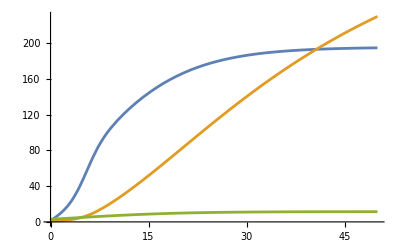

```mathematica
Module[{f=0.49,ϕ=4.09,pd=1/17.15,ν=0.05,δi=0.139,δm=0.0272,ρ=0.1235,pi=0.0005,K=55,Di0=1,Dm0=1,B0=3},eqs=NDSolve[{Di'[t]==f ϕ Dm[t](B[t]-pd Di[t])-(δi+ν)Di[t],Dm'[t]==ν Di[t]-δm Dm[t],B'[t]==ρ B[t](1-B[t]/K)-pi B[t]*Di[t],Di[0]==Di0,Dm[0]==Dm0,B[0]==B0},{Di,Dm,B},{t,0,50},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];Plot[Evaluate[{Di[t],Dm[t],B[t]}/.eqs],{t,0,50}]]
```

Modelo de la diapositiva 6/34 - tomando D’m[t] = cte, es decir, sin considerar a los adultos como una población independiente.

NDSolve::ndstf: At t == 29.849, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

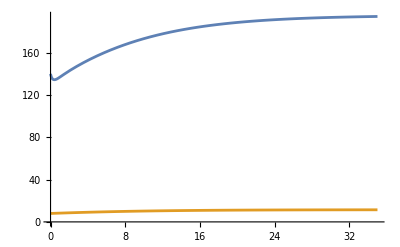

```mathematica
Module[{f=0.49,ϕ=4.09,pd=1/17.15,ν=0.05,δi=0.139,δm=0.0272,ρ=0.1235,pi=0.0005,K=55,Di0=140,B0=8},eqs=NDSolve[{Di'[t]==f ϕ ((ν Di[t]-5.5)/δm)(B[t]-pd Di[t])-(δi+ν)Di[t],B'[t]==ρ B[t](1-B[t]/K)-pi B[t]*Di[t],Di[0]==Di0,B[0]==B0},{Di,Dm,B},{t,0,35},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];Plot[Evaluate[{Di[t],B[t]}/.eqs],{t,0,35}]]
```

Modelo de la diapositiva 6/34 - tomando D' m[t] = cte, pero con un valor distinto de la cte en tres momentos distintos.

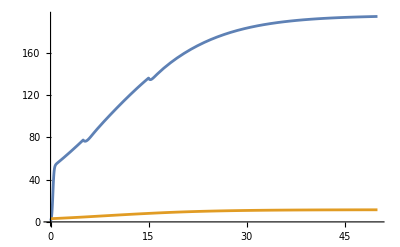

```mathematica
Module[{f=0.49,ϕ=4.09,pd=1/17.15,ν=0.05,δi=0.139,δm=0.0272,ρ=0.1235,pi=0.0005,K=55,Di0=1,B0=3},eqs=NDSolve[{Di'[t]==f ϕ ((ν Di[t]-Piecewise[{{0,t<5},{3,t>=5&&t<=15},{5.5,t>15}}])/δm)(B[t]-pd Di[t])-(δi+ν)Di[t],B'[t]==ρ B[t](1-B[t]/K)-pi B[t]*Di[t],Di[0]==Di0,B[0]==B0},{Di,Dm,B},{t,0,50},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];Plot[Evaluate[{Di[t],B[t]}/.eqs],{t,0,50}]]
```

Modelo nuevo dos poblaciones.

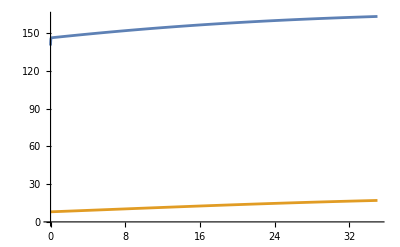

```mathematica
Module[{f=0.49,ϕ=4.09,pd=1/17.15,ν=0.05,δi=0.139,δm=0.0272,ρ=0.1235,pi=0.0005,K=55,Di0=140,B0=8},
r1=f*ϕ*(5.5*pd/δm) -(δi+ν);b12=f*ϕ*ν/δm;a1=f*ϕ*ν*pd/δm;c1=0.005;c3=0;
r2=ρ;b21=-pi;a2=ρ/K;c2=0.005;
eqs=NDSolve[{
(* Di'[t]==f ϕ ((ν Di[t]-5.5)/δm)(B[t]-pd Di[t])-(δi+ν)Di[t] *)
x1'[t]==x1[t]*(r1+b12*x2[t]-(a1+c1*b12*x2[t])*x1[t])+x2[t]*c3*f ϕ *(-5.5)/δm,
(* B'[t]==ρ B[t](1-B[t]/K)-pi B[t]*Di[t] *)
x2'[t]==x2[t]*(r2+b21*x1[t]-(a2+c2*b21*x1[t])*x2[t]),
x1[0]==Di0,
x2[0]==B0},
{x1,x2},{t,0,35},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];Plot[Evaluate[{x1[t],x2[t]}/.eqs],{t,0,35}]]
```

Modelo nuevo tres poblaciones.

| x1 | x2 | x3 | 
ri | 0.756168 | 0.1235 | -0.01 | 
ai | 0.00859244 | 0.00224545 | 0.01 | 
ci | 0.005 | 0.005 | 0.005 | 
 | b12 | b21 | b13 | b31
bij | 0.14736 | -0.0005 | -0.01 | 0.01

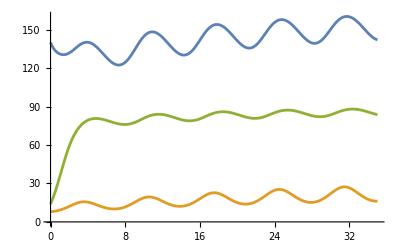

```mathematica
Module[{f=0.49,ϕ=4.09,pd=1/17.15,ν=0.05,δi=0.139,δm=25*0.0272,ρ=0.1235,pi=0.0005,K=55,Di0=140,B0=8,x30=14,tt=35},
r1=f*ϕ*(5.5*pd/δm) -(δi+ν);b12=f*ϕ*ν/δm;a1=f*ϕ*ν*pd/δm;c1=0.005;cx=0*f ϕ *(-5.5)/δm;
r2=ρ;b21=-pi;a2=ρ/K;c2=0.005;fo=2;
r3=-0.01;b13=-0.01;b31=0.01;a3=0.01;c3=0.005;
eqs=NDSolve[{
(* Di'[t]==f ϕ ((ν Di[t]-5.5)/δm)(B[t]-pd Di[t])-(δi+ν)Di[t] *)
x1'[t]==x1[t]*(r1+b12*x2[t]+b13*x3[t]-(a1+c1*(b12*x2[t]+b13*x3[t]))*x1[t])+x2[t]*cx,
(* B'[t]==ρ B[t](1-B[t]/K)-pi B[t]*Di[t] *)
x2'[t]==x2[t]*(r2*(1+fo*Sin[2*π*t/7])+b21*x1[t]-(a2+c2*b21*x1[t])*x2[t]),
x3'[t]==x3[t]*(r3+b31*x1[t]-(a3+c3*b31*x1[t])*x3[t]),
x1[0]==Di0,
x2[0]==B0,
x3[0]==x30},
{x1,x2,x3},{t,0,tt},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];
Print@TableForm[{{"","x1","x2","x3"},{"ri",r1,r2,r3},{"ai",a1,a2,a3},{"ci",c1,c2,c3},{"","b12","b21","b13","b31"},{"bij",b12,b21,b13,b31}}];
Plot[Evaluate[{x1[t],x2[t],x3[t]}/.eqs],{t,0,tt}]]
```

```mathematica
[{x1[t],x2[t],x3[t],x4[t]}/.eqs],{t,0,tt},PlotLegends->{"D","B","P","S"}
```

## Modelo nuevo cuatro poblaciones.

```mathematica
Module[{f=0.49,ϕ=4.09,pd=1/17.15,ν=0.05,δ=0.139,δm=25*0.0272,ρ=0.1235,pi=0.0005,K=55,Di0=10,B0=60,x30=20,x40=30,tt=50,μ=0.01,α=0.01,γ=0.01,λ=0.01,β=0.02,ρs=0.01,as=0.01,cs=0.005},
r1=-δ*0.1;b12=0.01*ϕ;a1=1*as+0*ϕ*pd;c1=cs;
r2=-μ;b21=-pi*10;b24=α;a2=1*as+0*ρ/K;c2=cs;
r3=-γ;b13=-ν;b31=λ;a3=as;c3=cs;
r4=ρs;b42=β;a4=1*as+0*ρs/K;c4=cs;
eqs=NDSolve[{
(* D'[t]==ϕ*D[t]*(B[t]-pd*D[t])-(δ+ν*P[t])*D[t] *)
x1'[t]==x1[t]*(r1+b12*x2[t]+b13*x3[t]-(a1+c1*(b12*x2[t]+b13*x3[t]))*x1[t]),
(* B'[t]==α*B[t]*S[t]-μ*B[t]-pi*B[t]*D[t] *)
x2'[t]==x2[t]*(r2+b21*x1[t]+b24*x4[t]-(a2+c2*(b21*x1[t]+b24*x4[t]))*x2[t]),
(* P'[t]==λ*P[t]*D[t]-γP[t] *)
x3'[t]==x3[t]*(r3+b31*x1[t]-(a3+c3*b31*x1[t])*x3[t]),
(* S'[t]==ρs*S[t](1-S[t]/K)-β*B[t]*S[t] *)
x4'[t]==x4[t]*(r4+b42*x2[t]-(a4+c4*b42*x2[t])*x4[t]),
x1[0]==Di0,
x2[0]==B0,
x3[0]==x30,
x4[0]==x40},
{x1,x2,x3,x4},{t,0,tt},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];
Print@TableForm[{{"","x1","x2","x3","x4"},{"ri",r1,r2,r3,r4},{"ai",a1,a2,a3,a4},{"ci",c1,c2,c3,c4},{"","b12","b21","b13","b31","b24","b42"},{"bij",b12,b21,b13,b31,b24,b42}}];
Plot[Evaluate[{x1[t],x2[t],x3[t],x4[t]}/.eqs],{t,0,tt},PlotLegends->{"D","B","P","S"},PlotRange->All]]
```

| x1 | x2 | x3 | x4 |  | 
ri | -0.0139 | -0.01 | -0.01 | 0.01 |  | 
ai | 0.01 | 0.01 | 0.01 | 0.01 |  | 
ci | 0.005 | 0.005 | 0.005 | 0.005 |  | 
 | b12 | b21 | b13 | b31 | b24 | b42
bij | 0.0409 | -0.005 | -0.05 | 0.01 | 0.01 | 0.02

```mathematica
(* más pruebas *)
```

Modelo con cuatro poblaciones editado.

```mathematica
Module[{f=0.49,ϕ=4.09,pd=1/17.15,ν=0.05,δ=0.139,δm=25*0.0272,ρ=0.1235,pi=0.0005,K=55,Di0=40,B0=100,x30=10,x40=30,tt=600,μ=0.01,α=0.01,γ=0.01,λ=0.01,β=0.02,ρs=0.01,as=0.00075,cs=0.005},
r1=-0.01;b12=0.02;b13=-0.001;a1=as;c1=cs;
r2=-0.15;b21=-0.01;b24=0.0036;a2=as;c2=cs;
r3=-0.01;b31=0.004;a3=as;c3=cs;
r4=0.15;b42=-0.0072;a4=as;c4=cs;
eqs=NDSolve[{
(* D'[t]==ϕ*D[t]*(B[t]-pd*D[t])-(δ+ν*P[t])*D[t] *)
x1'[t]==x1[t]*(r1+b12*x2[t]+b13*x3[t]-(a1+c1*(b12*x2[t]+b13*x3[t]))*x1[t]),
(* B'[t]==α*B[t]*S[t]-μ*B[t]-pi*B[t]*D[t] *)
x2'[t]==x2[t]*(r2+b21*x1[t]+b24*x4[t]-(a2+c2*(b21*x1[t]+b24*x4[t]))*x2[t]),
(* P'[t]==λ*P[t]*D[t]-γP[t] *)
x3'[t]==x3[t]*(r3+b31*x1[t]-(a3+c3*b31*x1[t])*x3[t]),
(* S'[t]==ρs*S[t](1-S[t]/K)-β*B[t]*S[t] *)
x4'[t]==x4[t]*(r4+b42*x2[t]-(a4+c4*b42*x2[t])*x4[t]),
x1[0]==Di0*0,
x2[0]==B0,
x3[0]==x30,
x4[0]==x40},
{x1,x2,x3,x4},{t,0,tt},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];
Print@TableForm[{{"","x1","x2","x3","x4"},{"ri",r1,r2,r3,r4},{"ai",a1,a2,a3,a4},{"ci",c1,c2,c3,c4},{"","b12","b21","b13","b31","b24","b42"},{"bij",b12,b21,b13,b31,b24,b42}}];
Plot[Evaluate[{x1[t],x2[t],x3[t],x4[t]}/.eqs],{t,0,tt},PlotLegends->{"D","B","P","S"},PlotRange->All]]
```

| x1 | x2 | x3 | x4 |  | 
ri | -0.01 | -0.15 | -0.01 | 0.15 |  | 
ai | 0.00075 | 0.00075 | 0.00075 | 0.00075 |  | 
ci | 0.005 | 0.005 | 0.005 | 0.005 |  | 
 | b12 | b21 | b13 | b31 | b24 | b42
bij | 0.02 | -0.01 | -0.001 | 0.004 | 0.0036 | -0.0072

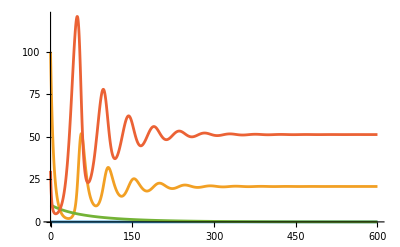

```mathematica
function[{r1_,b12_,b13_,a1_,c1_},{r2_,b21_,b24_,a2_,c2_},{r3_,b31_,a3_,c3_},{r4_,b42_,a4_,c4_}]:=Module[{Di0=40,B0=100,x30=10,x40=30,tt=600},
eqs=NDSolve[{
(* D'[t]==ϕ*D[t]*(B[t]-pd*D[t])-(δ+ν*P[t])*D[t] *)
x1'[t]==x1[t]*(r1+b12*x2[t]+b13*x3[t]-(a1+c1*(b12*x2[t]+b13*x3[t]))*x1[t]),
(* B'[t]==α*B[t]*S[t]-μ*B[t]-pi*B[t]*D[t] *)
x2'[t]==x2[t]*(r2+b21*x1[t]+b24*x4[t]-(a2+c2*(b21*x1[t]+b24*x4[t]))*x2[t]),
(* P'[t]==λ*P[t]*D[t]-γP[t] *)
x3'[t]==x3[t]*(r3+b31*x1[t]-(a3+c3*b31*x1[t])*x3[t]),
(* S'[t]==ρs*S[t](1-S[t]/K)-β*B[t]*S[t] *)
x4'[t]==x4[t]*(r4+b42*x2[t]-(a4+c4*b42*x2[t])*x4[t]),
x1[0]==Di0*0,
x2[0]==B0,
x3[0]==x30,
x4[0]==x40},
{x1,x2,x3,x4},{t,0,tt},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];
(*Print@TableForm[{{"","x1","x2","x3","x4"},{"ri",r1,r2,r3,r4},{"ai",a1,a2,a3,a4},{"ci",c1,c2,c3,c4},{"","b12","b21","b13","b31","b24","b42"},{"bij",b12,b21,b13,b31,b24,b42}}];*)
Plot[Evaluate[{x4[t],x2[t],x1[t],x3[t]}/.eqs],{t,0,tt},PlotLegends->{"Estimulos","Brotes","Parasito (Diaphora)","Parasitoides"},PlotRange->All]]
```

| x1 | x2 | x3 | x4 |  | 
ri | -0.01 | -0.15 | -0.01 | 0.15 |  | 
ai | 0.00075 | 0.00075 | 0.00075 | 0.00075 |  | 
ci | 0.005 | 0.005 | 0.005 | 0.005 |  | 
 | b12 | b21 | b13 | b31 | b24 | b42
bij | 0.02 | -0.01 | -0.001 | 0.004 | 0.0036 | -0.0072

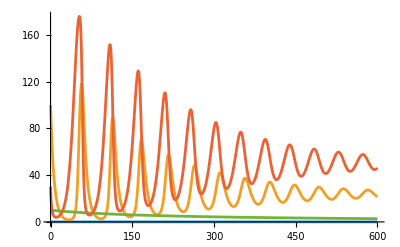

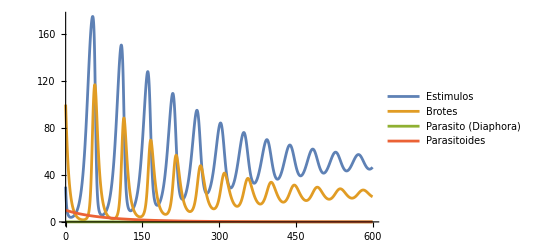

```mathematica
as=0.00044;cs=0.005;
j1={r1=-0.01,b12=0.02,b13=-0.001,a1=as,c1=cs};
j2={r2=-0.15,b21=-0.01,b24=0.0036,a2=a1,c2=c1};
j3={r3=-0.01,b31=0.004,a3=a1,c3=c1};
j4={r4=0.15,b42=-0.0072,a4=a1,c4=c1};
function[j1,j2,j3,j4]
```

```mathematica
Manipulate[
j1={r1,b12=0.02,b13=-0.001,a1=as,c1=cs};
j2={r2,b21=-0.01,b24=0.0036,a2=as,c2=cs};
j3={r3,b31=0.004,a3=as,c3=cs};
j4={r4,b42=-0.0072,a4=as,c4=cs};
function[j1,j2,j3,j4],
{as,0.00043,0.0005,0.000001},
{cs,0.001,0.0049,0.0000000001},
{r1,-10,10,0.01},
{r2,-0.15,10,0.01},
{r3,-0.01,0.1,0.01},
{r4,0.15,1.2,0.01}
]
```

```mathematica
Manipulate[
j1={r1,b12=0.02,b13=-0.001,a1=as,c1=cs};
j2={r2,b21=-0.01,b24=0.0036,a2=as,c2=cs};
j3={r3,b31=0.004,a3=as,c3=cs};
j4={r4,b42=-0.0072,a4=as,c4=cs};
function[j1,j2,j3,j4],
{as,0.00043,0.0005,0.000001},
{{cs,0.00305088},0.001,0.0049,0.0000000001},
{r1,-10,10,0.01},
{{r2,-0.073},-0.15,1,0.001},
{r3,-0.01,0.1,0.01},
{{r4,0.75},0.01,1.2,0.01}
]
```

```mathematica
1/as
```

2272.73

```mathematica
1/cs
```

200.

```mathematica
(*Probar estimulos y brotes, conseguir modelo base para jugar con las sgtes poblaciones. Checaar los signos de las r de los parametros de mas adelantes. Preguntar a Luciano nuevamente q significa 1/as y 1/cs*)
```

## Modelo con Di0 ≠ 0

```mathematica
function2[{r1_,b12_,b13_,a1_,c1_},{r2_,b21_,b24_,a2_,c2_},{r3_,b31_,a3_,c3_},{r4_,b42_,a4_,c4_},tt_]:=Module[{Di0=20,B0=50,x30=10,x40=40},
eqs=NDSolve[{
(* D'[t]==ϕ*D[t]*(B[t]-pd*D[t])-(δ+ν*P[t])*D[t] *)
x1'[t]==x1[t]*(r1+b12*x2[t]+b13*x3[t]-(a1+c1*(b12*x2[t]+b13*x3[t]))*x1[t]),
(* B'[t]==α*B[t]*S[t]-μ*B[t]-pi*B[t]*D[t] *)
x2'[t]==x2[t]*(r2+b21*x1[t]+b24*x4[t]-(a2+c2*(b21*x1[t]+b24*x4[t]))*x2[t]),
(* P'[t]==λ*P[t]*D[t]-γP[t] *)
x3'[t]==x3[t]*(r3+b31*x1[t]-(a3+c3*b31*x1[t])*x3[t]),
(* S'[t]==ρs*S[t](1-S[t]/K)-β*B[t]*S[t] *)
x4'[t]==x4[t]*(r4+b42*x2[t]-(a4+c4*b42*x2[t])*x4[t]),
x1[0]==Di0,
x2[0]==B0,
x3[0]==x30,
x4[0]==x40},
{x1,x2,x3,x4},{t,0,tt},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];
(*Print@TableForm[{{"","x1","x2","x3","x4"},{"ri",r1,r2,r3,r4},{"ai",a1,a2,a3,a4},{"ci",c1,c2,c3,c4},{"","b12","b21","b13","b31","b24","b42"},{"bij",b12,b21,b13,b31,b24,b42}}];*)
Plot[Evaluate[{x4[t],x2[t],x1[t],x3[t]}/.eqs],{t,0,tt},PlotLegends->{"4: Estimulos","2: Brotes","1: Parasito (Diaphora)","3: Parasitoides"},PlotRange->All]]
```

```mathematica
as=0.00044;cs=0.005;
```

```mathematica
Manipulate[
j1={r1,b12,b13,a1=as,c1=cs};
j2={r2,b21,b24,a2=as,c2=cs};
j3={r3,b31,a3=as,c3=cs};
j4={r4,b42,a4=as,c4=cs};
function2[j1,j2,j3,j4,200],
{as,0.00043,0.0005,0.000001},
{{cs,0.00305088},0.001,0.0049,0.000001},
{{r1,-0.1},-1,1,0.01},(*-7.73*)
{{r2,-0.064},-0.15,1,0.001},
{{r3,-0.001},-0.02,0.01,0.01},
{{r4,0.3},0.1,0.7,0.00001},
{{b12,0.02},0.01,0.1,0.001},
{{b13,-0.001},-0.002,-0.0001,0.0001},
{{b21,-0.001},-0.02,-0.001,0.0001},
{{b31,0.004},0,0.01,0.0001},
{{b24,0.0036},0.002,0.004,0.0001},
{{b42,-0.0072},-0.0080,-0.0070,0.00001}
]
```

```mathematica
Manipulate[
j1={r1,b12,b13,a1=as,c1=cs};
j2={r2,b21,b24,a2=as,c2=cs};
j3={r3,b31,a3=as,c3=cs};
j4={r4,b42,a4=as,c4=cs};
function2[j1,j2,j3,j4,200],
{{as,0.00001},0.0000001,0.001,0.00000000001},
{{cs,0.003091},0.001,0.009,0.000001},
{{r1,-0.5},-1,1,0.01},(*-7.73*)
{{r2,-0.031},-0.15,1,0.001},
{{r3,-0.0167},-0.02,0.01,0.0001},
{{r4,0.3127},0.1,0.7,0.00001},
{{b12,0.0131},0.01,0.1,0.001},
{{b13,-0.001},-0.002,-0.0001,0.0001},
{{b21,-0.0039},-0.02,-0.0001,0.0001},
{{b31,0.0008},0,0.01,0.0001},
{{b24,0.0035},0.002,0.004,0.0001},
{{b42,-0.00838},-0.0100,-0.0070,0.00001}
]
```

```mathematica
(*
periodo de tiempo: 60 dias
  4-2 oscilaciones
4-2-1, brotes deberian disminuir
 4-2-1-3, parasitoides regular parasitos

parasitoides: pocos que se sostengan en el tiempo que reduzcan parasitos en cantidad determinada. 
*)
```

```mathematica
Manipulate[
j1={r1,b12,b13,a1=as,c1=cs};
j2={r2,b21,b24,a2=as,c2=cs};
j3={r3,b31,a3=as,c3=cs};
j4={r4,b42,a4=as,c4=cs};
function2[j1,j2,j3,j4,200],
{{as,0.000699744},0.0000001,0.001,0.00000000001},
{{cs,0.00571},0.001,0.009,0.000001},
{{r1,-0.4},-1,1,0.01},(*-7.73*)
{{r2,0.025},-0.15,1,0.001},
{{r3,0.0067},-0.02,0.01,0.0001},
{{r4,0.30394},0.1,0.7,0.00001},
{{b12,0.013},0.01,0.1,0.001},
{{b13,-0.0007},-0.002,-0.0001,0.0001},
{{b21,-0.0032},-0.02,-0.0001,0.0001},
{{b31,0.0002},0,0.01,0.0001},
{{b24,0.0036},0.002,0.004,0.0001},
{{b42,-0.00838},-0.0100,-0.0070,0.00001}
]
```

```mathematica
{{as,0.00001},0.0000001,0.001,0.00000000001},
{{cs,0.003091},0.001,0.009,0.000001},
{{r1,-0.5},-1,1,0.01},(*-7.73*)
{{r2,-0.031},-0.15,1,0.001},
{{r3,-0.0167},-0.02,0.01,0.0001},
{{r4,0.3127},0.1,0.7,0.00001},
{{b12,0.0131},0.01,0.1,0.001},
{{b13,-0.001},-0.002,-0.0001,0.0001},
{{b21,-0.0039},-0.02,-0.0001,0.0001},
{{b31,0.0008},0,0.01,0.0001},
{{b24,0.0035},0.002,0.004,0.0001},
{{b42,-0.00838},-0.0100,-0.0070,0.00001}
```

```mathematica
Manipulate[
j1={r1,b12,b13,a1=as,c1=cs};
j2={r2,b21,b24,a2=as,c2=cs};
j3={r3,b31,a3=as,c3=cs};
j4={r4,b42,a4=as,c4=cs};
function2[j1,j2,j3,j4,200],
{{as,0.000699744},0.0000001,0.001,0.00000000001},
{{cs,0.00571},0.001,0.009,0.000001},
{{r1,-0.4},-1,1,0.01},(*-7.73*)
{{r2,0.025},-0.15,1,0.001},
{{r3,0.0067},-0.02,0.01,0.0001},
{{r4,0.30394},0.1,0.7,0.00001},
{{b12,0.013},0.01,0.1,0.001},
{{b13,-0.0007},-0.002,-0.0001,0.0001},
{{b21,-0.0032},-0.02,-0.0001,0.0001},
{{b31,0.0002},0,0.01,0.0001},
{{b24,0.0036},0.002,0.004,0.0001},
{{b42,-0.00838},-0.0100,-0.0070,0.00001}
]
```

## Modelo con Di0 ≠ 0

```mathematica
function3[{r1_,b12_,b13_,a1_,c1_},{r2_,b21_,b24_,a2_,c2_},{r3_,b31_,a3_,c3_},{r4_,b42_,a4_,c4_},{Di0_,B0_,x30_,x40_},tt_]:=Module[{eqs},
eqs=NDSolve[{
(* D'[t]==ϕ*D[t]*(B[t]-pd*D[t])-(δ+ν*P[t])*D[t] *)
x1'[t]==x1[t]*(r1+b12*x2[t]+b13*x3[t]-(a1+c1*(b12*x2[t]+b13*x3[t]))*x1[t]),
(* B'[t]==α*B[t]*S[t]-μ*B[t]-pi*B[t]*D[t] *)
x2'[t]==x2[t]*(r2+b21*x1[t]+b24*x4[t]-(a2+c2*(b21*x1[t]+b24*x4[t]))*x2[t]),
(* P'[t]==λ*P[t]*D[t]-γP[t] *)
x3'[t]==x3[t]*(r3+b31*x1[t]-(a3+c3*b31*x1[t])*x3[t]),
(* S'[t]==ρs*S[t](1-S[t]/K)-β*B[t]*S[t] *)
x4'[t]==x4[t]*(r4+b42*x2[t]-(a4+c4*b42*x2[t])*x4[t]),
x1[0]==Di0,
x2[0]==B0,
x3[0]==x30,
x4[0]==x40},
{x1,x2,x3,x4},{t,0,tt},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];
Plot[Evaluate[{x4[t],x2[t],x1[t],x3[t]}/.eqs],{t,0,tt},PlotLegends->{"4: Estimulos","2: Brotes","1: Parasito (Diaphora)","3: Parasitoides"},PlotRange->All]]
```

```mathematica
Manipulate[
j1={r1,b12,b13,a1=as,c1=cs};
j2={r2,b21,b24,a2=as,c2=cs};
j3={r3,b31,a3=as,c3=cs};
j4={r4,b42,a4=as,c4=cs};
x0={10,50,0,40};(*{x1:Di0,x2:B0,x3:x30,x4:x40}*)
function3[j1,j2,j3,j4,x0,360],
{{as,0},0.000,0.00043,0.000001},
{{cs,0.000485},0.000,0.0049,0.000001},
{{r1,-0.85},-2,1,0.01},(*-7.73*)
{{r2,-0.011},-0.15,1,0.001},
{{r3,-0.01},-0.02,0.01,0.01},
{{r4,0.30643},0.1,0.7,0.00001},
{{b12,0.02},0.001,0.1,0.0001},
{{b13,-0.0014},-0.002,-0.0001,0.0001},
{{b21,-0.0014},-0.02,-0.0001,0.00001},
{{b31,0.0006},0,0.01,0.0001},
{{b24,0.002},0.002,0.004,0.0001},
{{b42,-0.00719},-0.0080,-0.0020,0.00001}
]
```

```mathematica
(*
periodo de tiempo: 60 dias
  4-2 oscilaciones
4-2-1, brotes deberian disminuir
 4-2-1-3, parasitoides regular parasitos

parasitoides: pocos que se sostengan en el tiempo que reduzcan parasitos en cantidad determinada. 
*)
```

```mathematica
(*Ver casos: sin parasitoide, con parasitoide, con el doble, periodico*)
```